```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;
K2meV=1000*8.617332478*10^−5;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805"};
filesCh={"harm.C_4685_760","harm.C_4730_1900","harm.C_4759_2500","harm.C_4801_3200","harm.C_4850_3805"};
filesZrh={"harm.Zr_4685_760","harm.Zr_4730_1900","harm.Zr_4759_2500","harm.Zr_4801_3200","harm.Zr_4850_3805"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,5}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,5}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,5}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,5}];
```

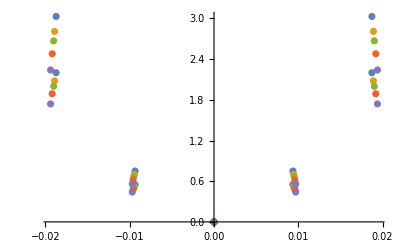

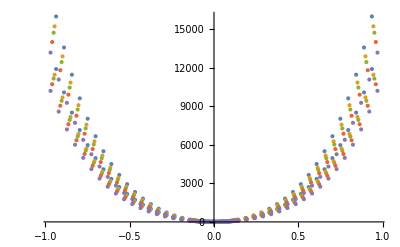

```mathematica
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;

(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,5}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]

(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,5}]
```

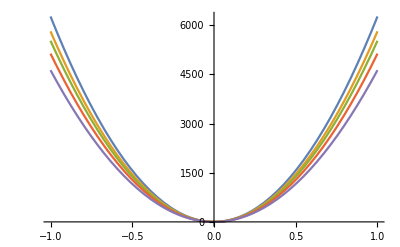

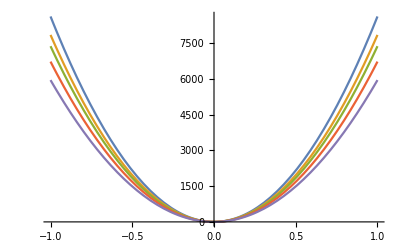

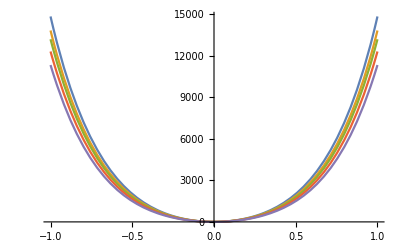

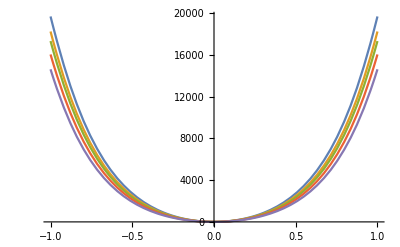

```mathematica
Plot[Evaluate@V[1,2,x],{x,-1,1}]
Plot[Evaluate@V[2,2,x],{x,-1,1}]
Plot[Evaluate@V[1,12,x],{x,-1,1}]
Plot[Evaluate@V[2,12,x],{x,-1,1}]
```

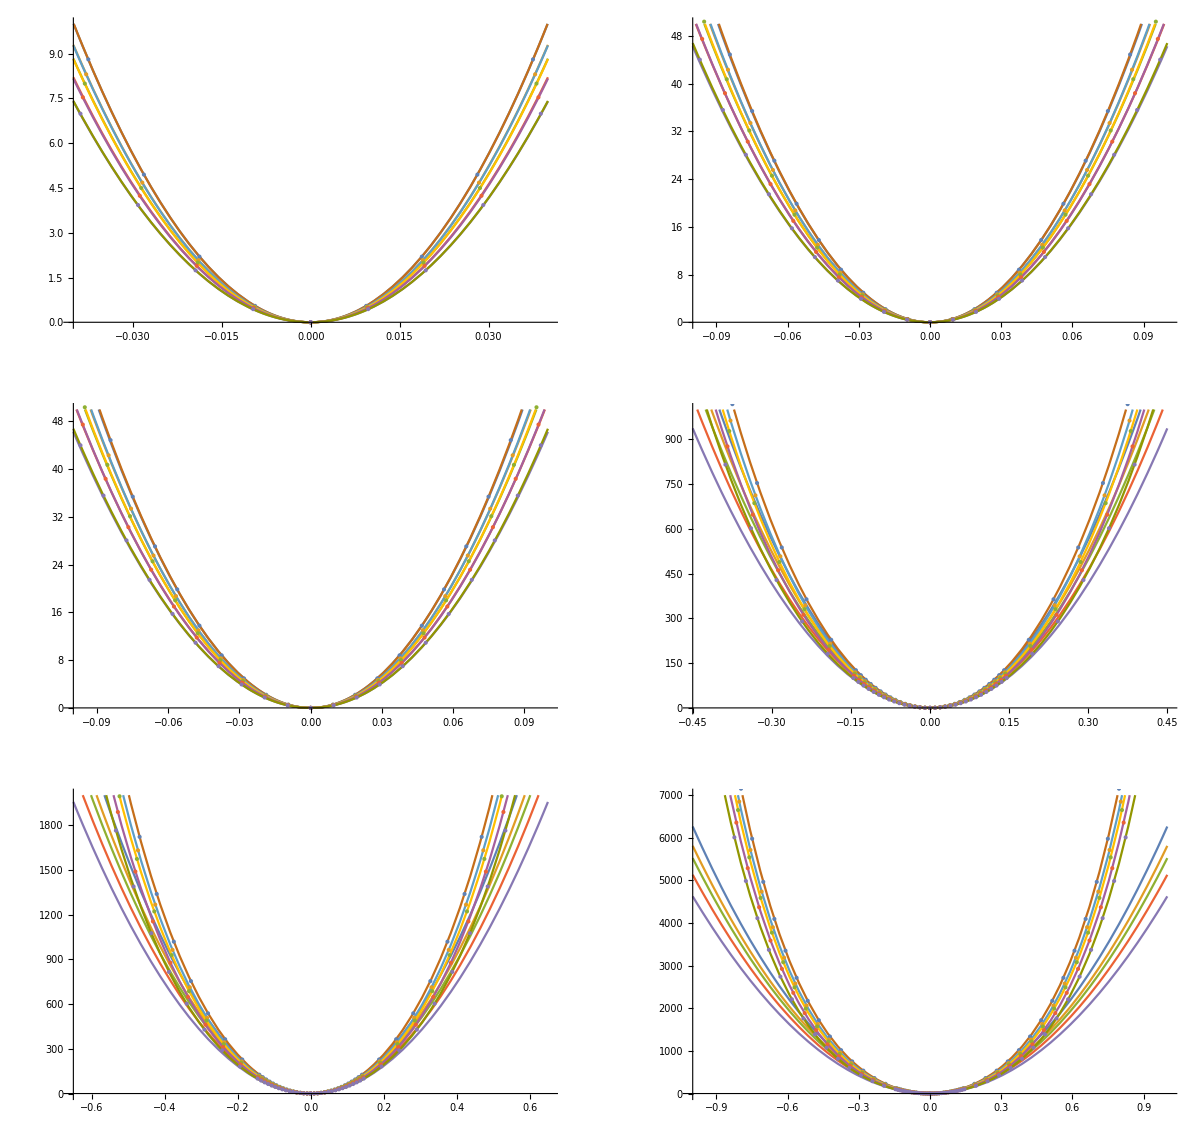

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@Cdata],Show[P0,ListPlot@Cdata]},{Show[P1,ListPlot@Cdata],Show[P2,ListPlot@Cdata]},{Show[P3,ListPlot@Cdata],Show[P4,ListPlot@Cdata]}},ImageSize->1200]
```

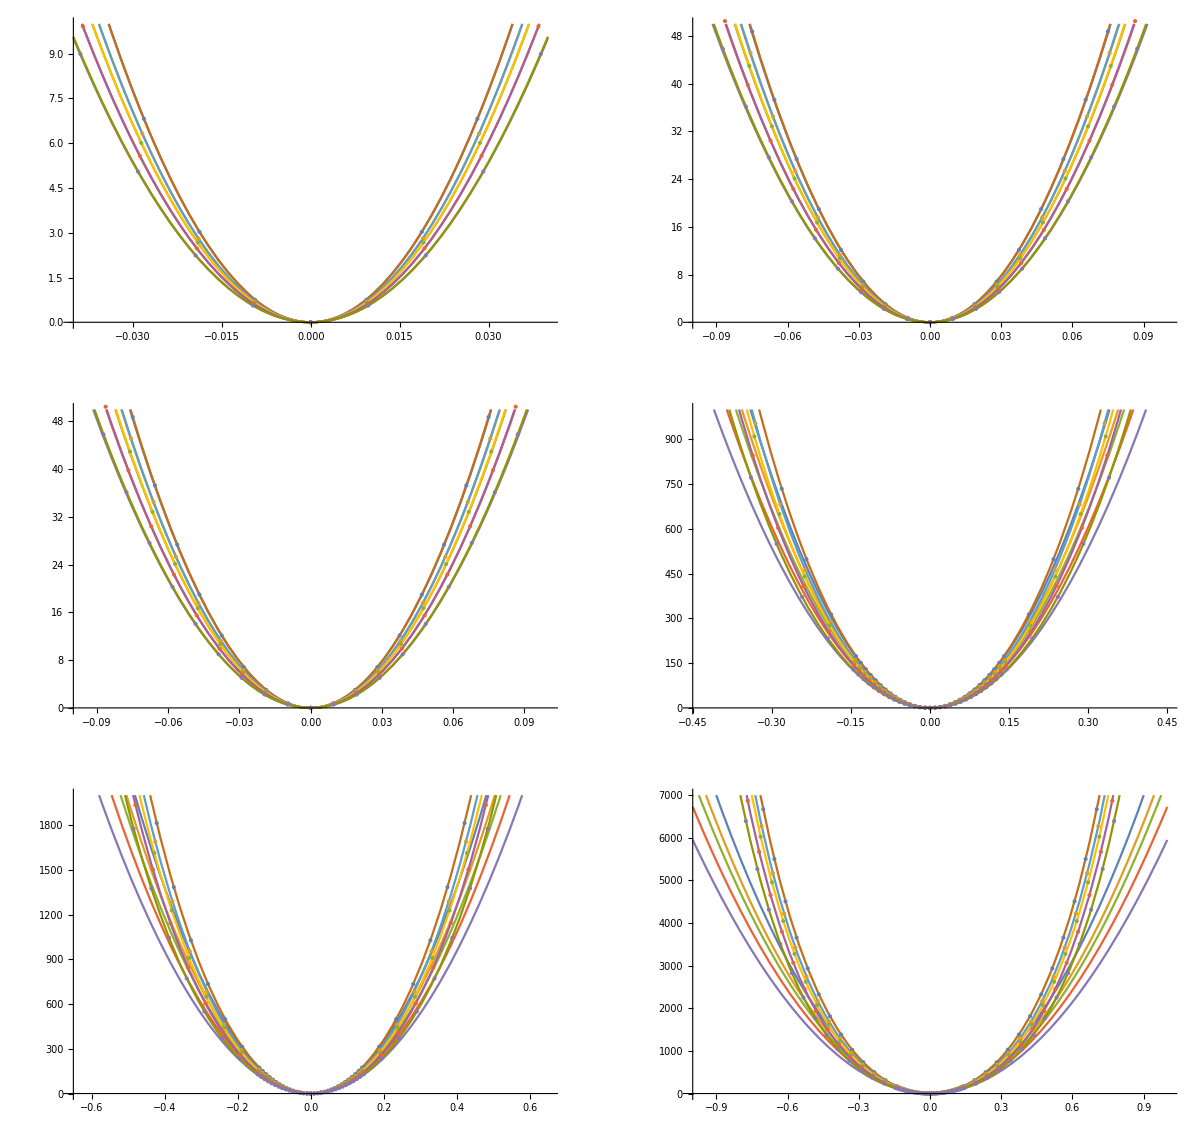

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@Zrdata],Show[P0z,ListPlot@Zrdata]},{Show[P1z,ListPlot@Zrdata],Show[P2z,ListPlot@Zrdata]},{Show[P3z,ListPlot@Zrdata],Show[P4z,ListPlot@Zrdata]}},ImageSize->1200]
```

```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46,5810.6,5523.05,5131.74,4626.36}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978,31.1058,30.3264,29.2323,27.7556}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8622.84,7848.26,7374.9,6727.43,5951.75}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.7495,13.1174,12.7156,12.1447,11.4231}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,2i,x]*u[x],{i,1,6,5}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,2i,x]*u[x],{i,1,6,5}];
```

```mathematica
Carbon and zirconium eigensystem solution
(*ℒallc[[harmonic=1,anharmonic=2]][[volumes1,2,3,4,5]*)

(*harmonic eigensystems*)
(*Carbon eigensystem*)
eigensysCh=Table[NDEigensystem[ℒallc[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZh=Table[NDEigensystem[ℒallz[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];

(*harmonic eigensystems*)
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒallc[[2]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[2]][[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,5}];
```

and Carbon eigensystem solution zirconium

```mathematica
(*eigensysCh[[vol]][[vals/vectors]]*)
(*Carbon harmonic and anharmonic spectrums*)

chrelspectrum=Table[(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5)/(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
crelspectrum=Table[(eigensysC[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5)/(eigensysCh[[vol]][[1]]/eigensysCh[[vol]][[1]][[1]]-0.5),{vol,1,5}];

cPrelspectrum=ListPlot[{chrelspectrum,
crelspectrum}];
(*Zr harmonic and anharmonic spectrums*)
zhrelspectrum=Table[(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5)/(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
zrelspectrum=Table[(eigensysZ[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5)/(eigensysZh[[vol]][[1]]/eigensysZh[[vol]][[1]][[1]]-0.5),{vol,1,5}];
```

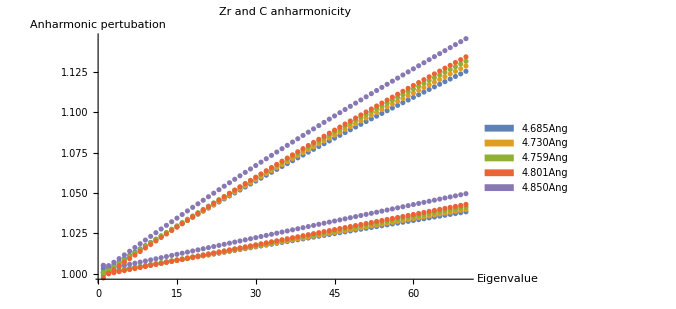

```mathematica
Show[ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]],ListPlot[crelspectrum],PlotRange->All,PlotLabel->"Zr and C anharmonicity",AxesLabel->{"Eigenvalue","Anharmonic \npertubation"},ImageSize->500]
```

```mathematica
(*cabron anharmonic fits*)
(**)
anhfitz1=Table[Fit[zrelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitz2=Table[Fit[zrelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitz3=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitz4=Table[Fit[zrelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitz1,anhfitz2},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz3},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
Show[Plot[{anhfitz2,anhfitz4},{x,1,140},PlotRange->All],ListPlot[zrelspectrum],ImageSize->1200];
```

{1.00022+0.000546816 x,0.999589+0.000576884 x,0.999758+0.000597169 x,0.998863+0.0006325 x,1.00199+0.000681324 x}

{1.00014+0.000553217 x-9.01551×10^-8 x^2,0.999491+0.000585002 x-1.14327×10^-7 x^2,0.999683+0.000603378 x-8.74551×10^-8 x^2,0.998712+0.000645027 x-1.76444×10^-7 x^2,1.00211+0.000671721 x+1.35251×10^-7 x^2}

{1.00026+0.00053517 x+5.4084×10^-7 x^2-5.92484×10^-9 x^3,0.999547+0.000575902 x+2.03823×10^-7 x^2-2.98732×10^-9 x^3,0.999765+0.000590016 x+3.79712×10^-7 x^2-4.38654×10^-9 x^3,0.998703+0.000646465 x-2.26731×10^-7 x^2+4.72176×10^-10 x^3,1.00246+0.000614143 x+2.14831×10^-6 x^2-1.8902×10^-8 x^3}

{1.00038+0.000503169 x+2.53565×10^-6 x^2-4.94206×10^-8 x^3+3.06308×10^-10 x^4,0.999596+0.000563038 x+1.00573×10^-6 x^2-2.04724×10^-8 x^3+1.23135×10^-10 x^4,0.999841+0.000569897 x+1.63388×10^-6 x^2-3.1733×10^-8 x^3+1.92581×10^-10 x^4,0.998669+0.000655438 x-7.86067×10^-7 x^2+1.26682×10^-8 x^3-8.58875×10^-11 x^4,1.00284+0.000512027 x+8.51393×10^-6 x^2-1.57701×10^-7 x^3+9.77457×10^-10 x^4}

```mathematica
(*Zr anharmonic fits*)
anhfitc1=Table[Fit[crelspectrum[[vol]],{1,x},x],{vol,1,5}]
anhfitc2=Table[Fit[crelspectrum[[vol]],{1, x, x^2},x],{vol,1,5}]
anhfitc3=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3},x],{vol,1,5}]
anhfitc4=Table[Fit[crelspectrum[[vol]],{1, x, x^2,x^3,x^4},x],{vol,1,5}]

(*Linear vs quadratic fits to anharmonic perturbation*)
(*Conclusion from different orders of fit to the anharmonic interaction shows quadratic wins*)
Show[Plot[{anhfitc1,anhfitc2},{x,1,140},PlotRange->All],ListPlot[crelspectrum],ImageSize->1200];
```

{1.00242+0.0017917 x,1.00108+0.00186071 x,1.00117+0.0019016 x,0.999284+0.00196949 x,1.00358+0.00206849 x}

{0.999737+0.0020154 x-3.15078×10^-6 x^2,0.998035+0.00211455 x-3.57522×10^-6 x^2,0.998108+0.00215669 x-3.59281×10^-6 x^2,0.996019+0.00224161 x-3.83263×10^-6 x^2,1.00057+0.00231952 x-3.53568×10^-6 x^2}

{0.999792+0.00200634 x-2.83398×10^-6 x^2-2.97465×10^-9 x^3,0.997851+0.00214462 x-4.62676×10^-6 x^2+9.87364×10^-9 x^3,0.997942+0.00218382 x-4.54145×10^-6 x^2+8.90738×10^-9 x^3,0.995663+0.00229967 x-5.86243×10^-6 x^2+1.90591×10^-8 x^3,1.00071+0.00229678 x-2.7405×10^-6 x^2-7.4665×10^-9 x^3}

{1.00009+0.0019285 x+2.01836×10^-6 x^2-1.08777×10^-7 x^3+7.45088×10^-10 x^4,0.997931+0.00212354 x-3.31268×10^-6 x^2-1.87793×10^-8 x^3+2.01781×10^-10 x^4,0.99804+0.0021578 x-2.91923×10^-6 x^2-2.64642×10^-8 x^3+2.49096×10^-10 x^4,0.995529+0.00233517 x-8.0754×10^-6 x^2+6.73117×10^-8 x^3-3.39807×10^-10 x^4,1.00115+0.00217981 x+4.55086×10^-6 x^2-1.66451×10^-7 x^3+1.11961×10^-9 x^4}

```mathematica
fanhc[x_]:=anhfitc2/.x->x
fanhz[x_]:=anhfitz2/.x->x
cOmega0
zOmega0
fanhcOmega[x_]:=anhfitc2*cOmega0/.x->x
fanhzOmega[x_]:=anhfitz2*zOmega0/.x->x
```

{32.2978,31.1058,30.3264,29.2323,27.7556}

{13.7495,13.1174,12.7156,12.1447,11.4231}

```mathematica
s0=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,10},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s1=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,50},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s2=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,200},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum]];
s3=Show[Plot[{Evaluate@fanhc[x],Evaluate@fanhz[x]},{x,1,300},ImageSize->800],ListPlot[crelspectrum],ListPlot[zrelspectrum,PlotLegends->SwatchLegend[{"4.685Ang","4.730Ang","4.759Ang","4.801Ang","4.850Ang"}]]];

GraphicsGrid[{{s0,s1,s2,s3}}]
```

-Graphics-

```mathematica
free[T_,spectrumZ_,spectrumC_,maxEigen_]:=-K2meV*1.5*T*Log[{Total[Exp[-2*Table[((0.5+x)*(spectrumZ)),{x,0,maxEigen}]/(K2meV*T)]],Total[Exp[-2*Table[((0.5+x)*(spectrumC)),{x,0,maxEigen}]/(K2meV*T)]]}]
```

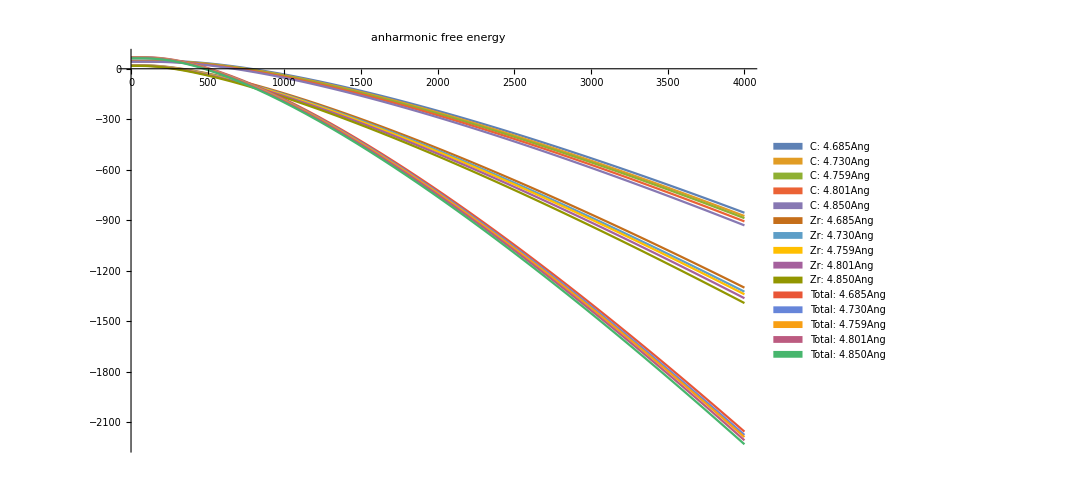

```mathematica
Plot[{Evaluate@(free[T,fanhcOmega[x],fanhzOmega[x],100]),Evaluate@Total@(free[T,fanhcOmega[x],fanhzOmega[x][[1]],100])}
,{T,1,4000},ImageSize->800,PlotLabel->"anharmonic free energy",PlotLegends->SwatchLegend[{"C: 4.685Ang","C: 4.730Ang","C: 4.759Ang","C: 4.801Ang","C: 4.850Ang","Zr: 4.685Ang","Zr: 4.730Ang","Zr: 4.759Ang","Zr: 4.801Ang","Zr: 4.850Ang","Total: 4.685Ang","Total: 4.730Ang","Total: 4.759Ang","Total: 4.801Ang","Total: 4.850Ang"}]]
```

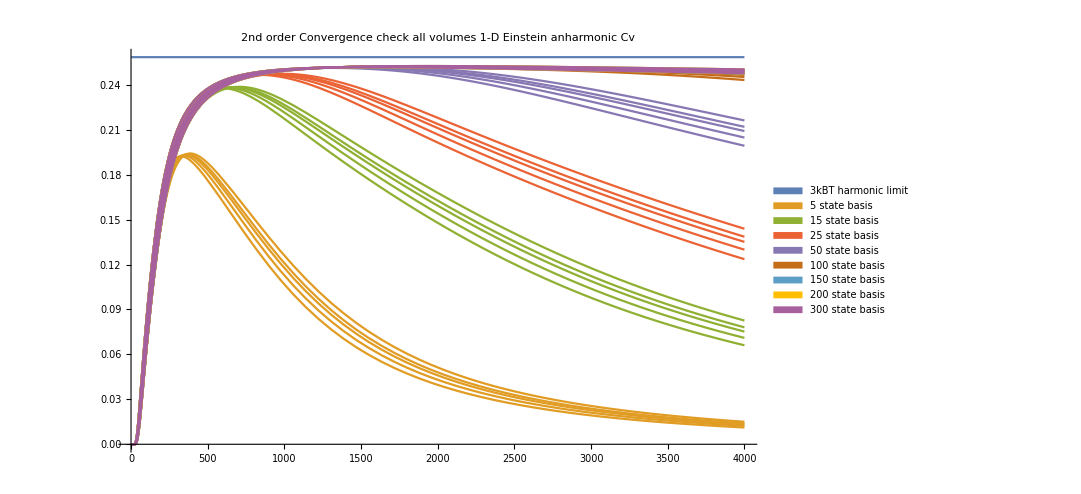

```mathematica
Plot[{K2meV*3,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],5],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],15],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],25],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],50],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],150],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]]/.T->t,Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],300],T],T]]/.T->t},{t,1,4000},PlotRange->All,ImageSize->800,PlotLabel->"2nd order Convergence check all volumes 1-D Einstein anharmonic Cv",PlotLegends->SwatchLegend[{"3kBT harmonic limit","5 state basis","15 state basis","25 state basis","50 state basis","100 state basis","150 state basis","200 state basis","300 state basis"}]]
```

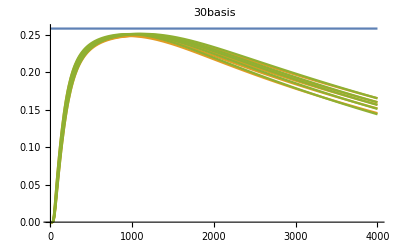

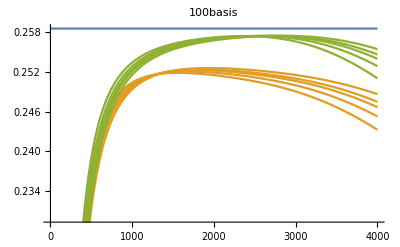

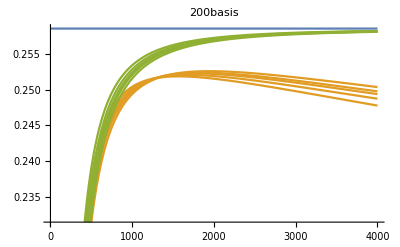

```mathematica
(*All volumes anharmonic harmonic heat capcity comparison 30 basis*)
pha0=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],30],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"]
(**PlotLegends->SwatchLegend[{"3kB","anharmonic 4.685Ang","anharmonic 4.730Ang","anharmonic 4.759Ang","anharmonic 4.801Ang","anharmonic 4.850Ang","harmonic 4.685Ang","harmonic 4.730Ang","harmonic 4.759Ang","harmonic 4.801Ang","harmonic 4.850Ang"}*)
(*All volumes anharmonic harmonic heat capcity comparison 100 basis*)
pha1=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],100],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,100],T],T]])/.T->t},{t,1,4000},PlotLabel->"100basis"]
(*All volumes anharmonic harmonic heat capcity comparison 200 basis*)
pha2=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,200],T],T]])/.T->t},{t,1,4000},PlotLabel->"200basis"]
(*All volumes anharmonic harmonic heat capcity comparison 300 basis*)
pha3=Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],300],T],T]])/.T->t,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,300],T],T]])/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"3kB","anharmonic all volumes","harmonic all volumes"}],PlotLabel->"300basis"]
```

```mathematica
GraphicsGrid[{{pha0,pha1,pha2}},ImageSize->2500]
```

-Graphics-

```mathematica
cvPerturb=(T*D[-D[free[T,fanhcOmega[x],fanhzOmega[x],200],T],T]-T*D[-D[free[T,cOmega0,zOmega0,200],T],T]);
```

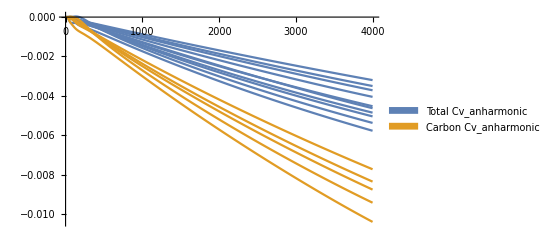

```mathematica
Plot[{Evaluate@cvPerturb/.T->t,Total[cvPerturb]/.T->t},{t,1,4000},PlotLegends->SwatchLegend[{"Carbon Cv_anharmonic","Carbon Cv_anharmonic","Total Cv_anharmonic"}]]
```

```mathematica
(*Import QHA dS/dV and dV/dT to convert Cv to Cp*)
```

```mathematica
temps={760,1900,2500,3200,3805};
anCv=Total[cvPerturb]/.T->temps
```

{{-0.00166808,-0.00399446,-0.00512792,-0.00638195,-0.00741046},{-0.00179667,-0.00434968,-0.00557408,-0.00692062,-0.00801819},{-0.0018958,-0.00457085,-0.0058535,-0.00726286,-0.00840956},{-0.00204324,-0.00496362,-0.00634162,-0.007845,-0.00905783},{-0.00231621,-0.00545307,-0.00697273,-0.00864288,-0.00999266}}

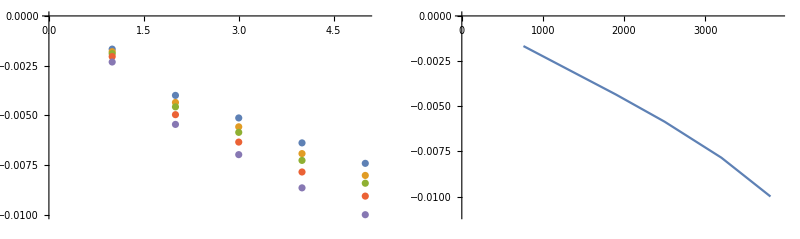

```mathematica
GraphicsGrid[{{ListPlot@anCv,ListPlot[Transpose@{temps,Table[anCv[[i]][[i]],{i,1,5}]},PlotRange->{{0,3900},{-0.011,0}},Joined->True]}},ImageSize->800]
```

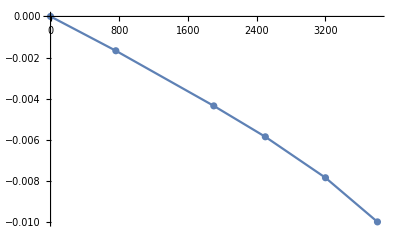

-0.0000586675-1.86577×10^-6 T-1.89438×10^-10 T^2

```mathematica
anCvdata=Partition[Flatten@{{0,0},Transpose[{temps,Table[anCv[[i]][[i]],{i,1,5}]}]},2];
Show[ListPlot[anCvdata],ListPlot[anCvdata,Joined->True]]
Cvanfit=Fit[anCvdata,{1,T,T^2},T]
```

```mathematica
(*Cp=Cv+T*dV/dT*dS/dV*)
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
normal=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,1,8}];
```

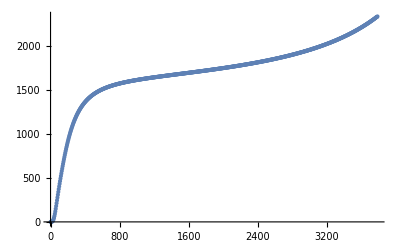

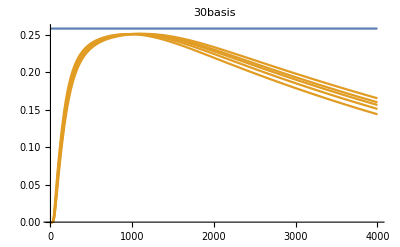

```mathematica
ListPlot[normal[[7]]]
Plot[{K2meV*3,Evaluate@(Total[T*D[-D[free[T,cOmega0,zOmega0,30],T],T]])/.T->t},{t,1,4000},PlotLabel->"30basis"]
```

```mathematica
kjmol2evatom=1/(96.487*64);
qhaCpeVatom=Transpose[{Transpose[normal[[7]]][[1]],Transpose[normal[[7]]][[2]]*kjmol2evatom}];
interQhaCp[T_]:=Interpolation[qhaCpeVatom][T]
```

```mathematica
harmCv[T_]:=1.5*(K2meV*((((2cOmega0[[1]]))/(K2meV*T))^2)*Exp[((2cOmega0[[1]]))/(K2meV*T)]/((Exp[((2cOmega0[[1]]))/(K2meV*T)]-1)^2)+K2meV*((((2zOmega0[[1]]))/(K2meV*T))^2)*Exp[((2zOmega0[[1]]))/(K2meV*T)]/((Exp[((2zOmega0[[1]]))/(K2meV*T)]-1)^2))
```

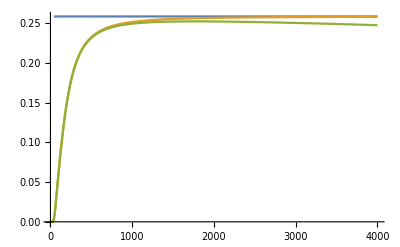

```mathematica
Plot[{3K2meV,harmCv[T],harmCv[T]+Cvanfit/.T->T},{T,1,4000},PlotRange->All]
```

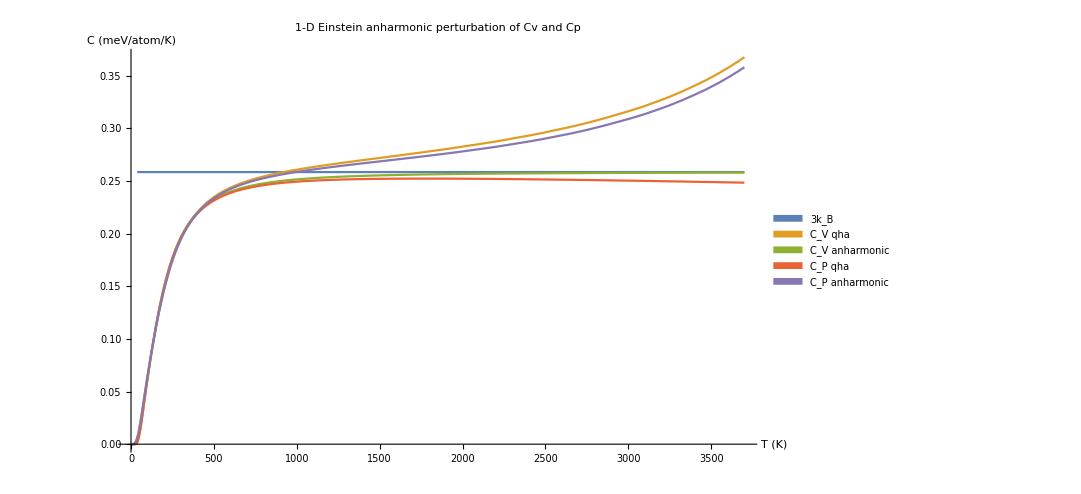

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{3K2meV,interQhaCp[T],harmCv[T],harmCv[T]+Cvanfit/.T->T,interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotRange->All,PlotLabel->"1-D Einstein anharmonic perturbation of Cv and Cp",PlotLegends->SwatchLegend[{"3k_B","C_V qha","C_V anharmonic","C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"}]
```

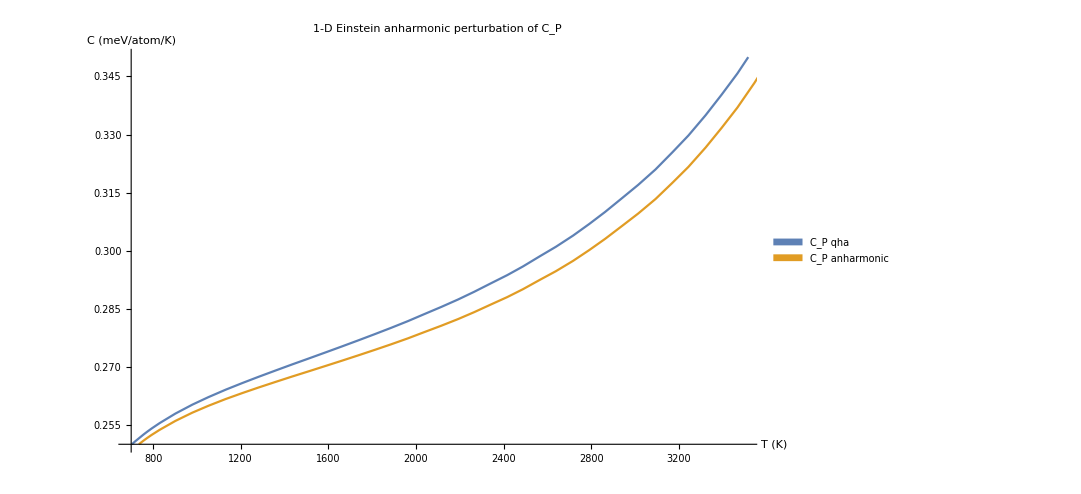

```mathematica
(*Plot the volume dependent anharmonic pertubuation of Cv and Cp*)
Plot[{interQhaCp[T],interQhaCp[T]+Cvanfit/.T->T},{T,1,3700},PlotLabel->"1-D Einstein anharmonic perturbation of C_P",PlotLegends->SwatchLegend[{"C_P qha","C_P anharmonic"}],ImageSize->800,AxesLabel->{"T (K)","C (meV/atom/K)"},PlotRange->{{700,3500},{0.25,0.35}}]
```